```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Options

```mathematica
usePotForDensPot=False;(*For many orbits, the potential above FAST is not the total potential. For orbit 1612, there are ion beams throughout the observed period indicating the existence of a potential structure above FAST. (On the other hand for orbit 1607, for example, the potential above DOES appear to be the whole potential, because there are no observed ion beams.) *)
```

### Load data

```mathematica
fName="20180524-orb1612_mathematica_kappa.txt";
```

```mathematica
fName="20180524-orb1612_mathematica_kappa__1_25sRate.csv";
fName="20180813-orb_1612-sRate1_25-autoIonBeamIdent-Mathematica.csv";
fName="20180813-orb_1612-sRate1_25-autoIonBeamIdent-twoBelowPeak-Mathematica.csv";
fName="20180813-orb_4862-densPA_30-Mathematica.csv";
fName="20180813-orb_4862-densPA_45-Mathematica.csv";
fName="20180813-orb_4862-densPA_36-Mathematica.csv";
fName="20180813-orb_4862-densPA_36-MathematicaFINALQQ.csv";
(*fName="20180813-orb_4862-densPA_60-Mathematica.csv";*)
(*fName="20180810-orb_1612-sRate1_25-Mathematica.csv"*)
```

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];(*
data=Cases[Import[inDir<>fName,"Table"],{_?NumberQ,___}];
data=Cases[Import[inDir<>fName,"Table"],{_?StringQ,___}]*)
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPot,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

```mathematica
potTFactor = 0;
```

```mathematica
curs=curs*-1;
```

```mathematica
dens = dens*3;
```

```mathematica
densErrs = densErrs*3;
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
(*{"12:00:29.7","12:00:37.4"},*)
(*{{"12:00:28.5","12:00:37.4"},{"12:00:41.0","12:00:48"}},*)
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
(*{"12:01:22.7","12:01:29.7"}*)
{"09:06:31.288","09:06:51.463"} (*Orbit 4682*)
(*{"12:01:22.7","12:01:29.7"}*) (*BEST?*)
(*{"12:01:20.4","12:01:29.7"}*)
(*{"12:01:17.1","12:01:23.4"}*)];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
{time[[#]]}&/@itvlBounds
```

Part::partd: Part specification time⟦21⟧ is longer than depth of object.

Part::partd: Part specification time⟦29⟧ is longer than depth of object.

{{time⟦21⟧},{time⟦29⟧}}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

#### Manipulate to figure

```mathematica
{mType1,mType3}={1,"Manip"};
```

```mathematica
pRange={{000,1400},{0,3}};
```

```mathematica
pRange={{000,Max[pots]*1.1},{0,Max[curs]*1.1}};
```

```mathematica
pRangeJe={{000,Max[pots]*1.1},{0,Max[jes]*1.2}};
```

```mathematica
If[ValueQ[dens]&&ValueQ[densPot],pRangeDens={{000,Max[densPot]*1.1},{0,Max[dens]*1.2}};]
```

```mathematica
manipInds=inds1;
ind1Start=1;ind1Init=manipInds[[1]];ind1EndInit=manipInds[[Round@(Length@manipInds/2)]];ind2Init=manipInds[[-1]];
```

```mathematica
mType=1;
```

```mathematica
mType="Manip";
```

```mathematica
time=tids;
```

```mathematica
Switch[mType,
mType1,
Row[{tPlotInds2[inds1,curs,curErrs,pRange,tids,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds2[inds1,jes,jeErrs,pRangeJe,tids,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType3,
Manipulate[Manipulate[
Row[{tPlotRange[ind1,ind2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotRange[ind1,ind2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]
```

### Get in Monte Carlo-able format

```mathematica
tid=tids[[inds1]];
```

```mathematica
{jData}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
{jErrData}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
{jWt}=(1/(curErrs[[#]])^2)&/@{inds1};
```

```mathematica
potErr=potErrs[[inds1]];
curErr=curErrs[[inds1]];
```

```mathematica
If[ValueQ[dens],
If[usePotForDensPot,densPot=pots;];
{densData}=(Partition[Riffle[densPot[[#]]+potTFactor,dens[[#]]],2])&/@{inds1};
{densErrData}=(makeErrorData[densPot[[#]]+potTFactor,dens[[#]],densErrs[[#]]])&/@{inds1};
{densWt}=(1/(densErrs[[#]])^2)&/@{inds1};
]
densPotErr=densPotErrs[[inds1]];
```

Energy flux data

```mathematica
{jeData}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1};
```

```mathematica
{jeErrData}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1};
```

```mathematica
{jeWt}=(1/(jeErrs[[#]])^2)&/@{inds1};
```

```mathematica
potVal=pots[[inds1]];
nPots=Length@potVal;
curVal=jData[[;;,2]];
```

#### Which fit method to use?

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

#### Bounds (NB: irrelevant if the parameter in question is fixed)

```mathematica
minFitT=115;
maxFitT=125;
minFitRB=5;
maxFitRB=1000;
minFitN=0.03;
maxFitN=2;
minFitKappa=Switch[interval,
1,3.84,
2,2.05];
maxFitKappa=35;
```

#### Init model setter uppers

Kappa

```mathematica
kappaFac[RB_Real,phiBar_Real,kappa_Real]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
Options[kFitVarSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{kFitN,kFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{kFitT,kFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{kFitRB,kFitRBinit}]];
If[OptionValue[fixKappa]==False,fitVars=Append[fitVars,{kFitKappa,kFitKappainit}]];
fitVars
]
```

```mathematica
Options[kConstraintSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<kFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<kFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<kFitRB<maxFitRB]];
If[OptionValue[fixKappa]==False,constraints=Append[constraints,minFitKappa<kFitKappa<maxFitKappa]];
constraints
]
```

```mathematica
Options[kFitJVModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitJVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitJeVModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitJeVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitTotalModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa->False,
DonVModel->False,DoJVModel->False,DoJeVModel->False};
kFitTotalModelSetup[OptionsPattern[]]:=Module[{fitModel,nVKappaFunc},
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
nVKappaFunc=nVKappa2p5;
(*nVKappaFunc=nVKappa;*)
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(kFitN*kappaFac[kFitRB/RBFASTtoIonos,pot/kFitT,kFitKappa])],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(kFitN*kappaFac[kFitRB/RBFASTtoIonos,pot/kFitT,kFitKappa])],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,Evaluate@(kFitN*kappaFac[kFitRB/RBFASTtoIonos,pot/kFitT,kFitKappa])],
OptionValue[DonVModel],
fitModel=(kFitN*kappaFac[kFitRB/RBFASTtoIonos,pot/kFitT,kFitKappa]),
OptionValue[DoJVModel],
fitModel=JVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa],
OptionValue[DoJeVModel],
fitModel=JEVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]]
;
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitOutputSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={kFitN,kFitT,kFitRB,kFitKappa,kFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitOutput=fitOutput/.{kFitKappa->OptionValue[fixKappa]}];
fitOutput
]
```

```mathematica
Options[kFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,kFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,kFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,kFitRB->OptionValue[fixRB]];];
If[NumberQ@OptionValue[fixKappa],fitValAdds=Append[fitValAdds,kFitKappa->OptionValue[fixKappa]];];
fitValAdds
]
```

```mathematica
Options[kDOFSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kDOFSetup[OptionsPattern[]]:=Module[{count},
count=4;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
If[NumberQ@OptionValue[fixKappa],count--];
count
]
```

```mathematica
Options[kFixStringSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
If[NumberQ@OptionValue[fixKappa],fixString=fixString<>(StringReplace[ToString@StringForm["-fixKappa`1`",OptionValue[fixKappa]],"."->"_"])];
fixString
]
```

Now Maxwellian setup

```mathematica
Options[gFitVarSetup]={fixT->False,fixN->False,fixRB-> False};
gFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{gFitN,gFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{gFitT,gFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{gFitRB,gFitRBinit}]];
fitVars
]
```

```mathematica
Options[gConstraintSetup]={fixT->False,fixN->False,fixRB-> False};
gConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<gFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<gFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<gFitRB<maxFitRB]];
constraints
]
```

```mathematica
Options[gFitnVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitnVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=nVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitJVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitJVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitJeVModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitJeVModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitTotalModelSetup]={fixT->False,fixN->False,fixRB-> False,
DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalModelSetup[OptionsPattern[]]:=Module[{fitModel},
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitModel=Which[
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,Evaluate@nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]],
OptionValue[DonVModel],
fitModel=nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN],
OptionValue[DoJVModel],
fitModel=JVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN],
OptionValue[DoJeVModel],
fitModel=JEVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]]
;
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitTotalDataSetup]={DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalDataSetup[nData_,jData_,jeData_,OptionsPattern[]]:=Module[{fitData},
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitData=Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}],
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitData=Join[jeData/.{x_,y_}->{2,x,y},nData/.{x_,y_}->{3,x,y}],
OptionValue[DonVModel],
fitData=nData,
OptionValue[DoJVModel],
fitData=jData,
OptionValue[DoJeVModel],
fitData=jeData];
fitData
]
```

```mathematica
Options[gFitTotalWeightSetup]={DonVModel->False,DoJVModel->False,DoJeVModel->False};
gFitTotalWeightSetup[nWts_,jWts_,jeWts_,OptionsPattern[]]:=Module[{fitWts},
Which[
OptionValue[DonVModel]&&OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitWts=jWts~Join~jeWts~Join~nWts,
OptionValue[DonVModel]&&OptionValue[DoJVModel],
fitWts=jWts~Join~nWts,
OptionValue[DoJVModel]&&OptionValue[DoJeVModel],
fitWts=jWts~Join~jeWts,
OptionValue[DonVModel]&&OptionValue[DoJeVModel],
fitWts=jeWts~Join~nWts,
OptionValue[DonVModel],
fitWts=nWts,
OptionValue[DoJVModel],
fitWts=jWts,
OptionValue[DoJeVModel],
fitWts=jeWts];
fitWts
]
```

```mathematica
Options[gFitOutputSetup]={fixT->False,fixN->False,fixRB-> False};
gFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={gFitN,gFitT,gFitRB,gFitKappa,gFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{gFitRB->OptionValue[fixRB]}];
fitOutput
]
```

```mathematica
Options[gFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False};
gFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,gFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,gFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,gFitRB->OptionValue[fixRB]];];
fitValAdds
]
```

```mathematica
Options[gDOFSetup]={fixT->False,fixN->False,fixRB-> False};
gDOFSetup[OptionsPattern[]]:=Module[{count},
count=3;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
count
]
```

```mathematica
Options[gFixStringSetup]={fixT->False,fixN->False,fixRB-> False};
gFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
fixString
]
```

```mathematica
Options[genMCStartupMessage]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
genMCStartupMessage[OptionsPattern[]]:=Module[{count},
Print[ToString@StringForm["Interval: `1`",interval]];
If[NumberQ@OptionValue[fixN],Print[ToString@StringForm["fixN    : `1`",OptionValue[fixN]]]];
If[NumberQ@OptionValue[fixT],Print[ToString@StringForm["fixT    : `1`",OptionValue[fixT]]]];
If[NumberQ@OptionValue[fixRB],Print[ToString@StringForm["fixRB   : `1`",OptionValue[fixRB]]]];
If[NumberQ@OptionValue[fixKappa],Print[ToString@StringForm["fixKappa: `1`",OptionValue[fixKappa]]]];
]
```

#### Now fixies

```mathematica
doFixT=True;
doFixKappa=False;
```

```mathematica
(*kfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,180],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,120,2,140],False,False];*)
kfixTVal:=Switch[doFixT,True,Switch[interval,1,124,2,93],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,102],False,False];
kfixNVal=False;
gfixNVal=False;
kfixRBVal= False;
gfixRBVal= False;
(*fixKappaVal=Switch[doFixKappa,True, Switch[interval,1,5.4,2,2.6],False,False];*)
fixKappaVal=Switch[doFixKappa,True, Switch[interval,1,5/2,2,2.05],False,False]; (*2018/06/07 Try kappa=5/2*)
```

#### What kind of models?

```mathematica
donVModel=True;
doJVModel = True;
doJeVModel=True;
```

#### Init models

```mathematica
kJVModel=kFitJVModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
kTotalModel=kFitTotalModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
gTotalModel=gFitTotalModelSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal,
DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
```

```mathematica
totalData=gFitTotalDataSetup[densData,jData,jeData,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
totalWts=gFitTotalWeightSetup[densWt,jWt,jeWt,DonVModel->donVModel,DoJVModel->doJVModel,DoJeVModel->doJeVModel];
```

```mathematica
kFitVars:=kFitVarSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitVars:=gFitVarSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kConstraints=kConstraintSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gConstraints=gConstraintSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitOutput:=kFitOutputSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitOutput:=gFitOutputSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitValAdds=kFitValAddsSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitValAdds=gFitValAddsSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kDOF=nPots-kDOFSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gDOF=nPots-gDOFSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFixString:=kFixStringSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFixString:=gFixStringSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kMCStartupMessage:=genMCStartupMessage[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gMCStartupMessage:=genMCStartupMessage[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

#### Initial fit

```mathematica
kinitParams = RandomReal/@{{minFitN,maxFitN},{minFitT,maxFitT},{minFitRB,maxFitRB},{minFitKappa,maxFitKappa}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
ginitParams = RandomReal/@{{minFitN,maxFitN},{minFitT,maxFitT},{minFitRB,maxFitRB}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
```

```mathematica
kInitialTotalFit=NonlinearModelFit[totalData,(If[Length@kConstraints≠0,{kTotalModel,kConstraints},kTotalModel]),kFitVars,{set,pot},Weights->totalWts,VarianceEstimatorFunction->(1&),Method->fitMethod];
gInitialTotalFit=NonlinearModelFit[totalData,(If[Length@gConstraints≠0,{gTotalModel,gConstraints},gTotalModel]),
gFitVars,
{set,pot},
Weights->totalWts,VarianceEstimatorFunction->(1&),Method->fitMethod];
```

```mathematica
(*kInitialTotalFit=NonlinearModelFit[totalData,(If[Length@kConstraints≠0,{kTotalModel,kConstraints},kTotalModel]),kFitVars,{pot},Weights->totalWts,VarianceEstimatorFunction->(1&),Method->fitMethod];
gInitialTotalFit=NonlinearModelFit[totalData,(If[Length@gConstraints≠0,{gTotalModel,gConstraints},gTotalModel]),
gFitVars,
{pot},
Weights->totalWts,VarianceEstimatorFunction->(1&),Method->fitMethod];*)
```

```mathematica
kInitialFitVals:=Append[Flatten@Append[kInitialTotalFit["BestFitParameters"],kFitValAdds],kFitChi2red->Total[(kInitialTotalFit["FitResiduals"])^2*totalWts]/kDOF]
```

```mathematica
gInitialFitVals:=Append[Flatten@Append[gInitialTotalFit["BestFitParameters"],gFitValAdds],gFitChi2red->Total[(gInitialTotalFit["FitResiduals"])^2*totalWts]/gDOF]
```

```mathematica
kInitialFitVals
gInitialFitVals
```

{kFitN→0.0943379,kFitRB→708.124,kFitKappa→23.8587,kFitT→93,kFitChi2red→5.03133}

{gFitN→0.098326,gFitRB→999.969,gFitT→102,gFitChi2red→4.24397}

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gTripleVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,4]/.gInitialFitVals};
kTripleVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,4]/.kInitialFitVals};
```

```mathematica
tripleParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gTripleVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kTripleVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
tripleTitle=StringJoin@Riffle[tids[[inds1[[{1,-1}]]]],"–"];
```

```mathematica
tripleFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[curs]*0.9,Max[curs]*1.1}},
Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",tripleTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[tripleParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
tripleFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gFitRB,gFitT,gFitN]/.gInitialFitVals,JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),
{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[jes]*0.9,Max[jes]*1.1}},
Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,nVKappa[pot,kFitRB/RBFASTtoIonos,kFitT,kFitN,kFitKappa]/.kInitialFitVals})),{pot,20,Max[pots]},PlotRange->{{Min[pots],Max[pots]},{Min[dens],Max[dens]}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];*)
```

```mathematica
kappaFac[RB_,phiBar_Real,kappa_]:=phiBar^(3/2)/(√π)Gamma[kappa+1]/((kappa-3/2)^(3/2)Gamma[kappa-1/2])(NIntegrate[√(Ebar+1)(1+(Ebar phiBar)/(kappa-3/2))^(-(kappa+1)),{Ebar,0,∞}]-1/(RB-1)NIntegrate[√(1-Ebar)(1+(Ebar phiBar)/((kappa-3/2) (RB-1)))^(-(kappa+1)),{Ebar,0,1}])
```

```mathematica
{kPlotN,kPlotRB,kPlotKappa,kPlotT,kPlotChi2red}=Values@kInitialFitVals;
```

```mathematica
tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,kPlotN*kappaFac[kPlotRB/RBFASTtoIonos,pot/kPlotT,kPlotKappa]/.kInitialFitVals})),{pot,20,Max[pots]*1.3},PlotRange->{{Min[pots]*0.9,Max[pots]*1.1},{Min[dens]*0.9,Max[dens]*1.1}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*tripleFitDensPlot=Plot[Evaluate@(({nVMaxwellian[pot,gFitRB/RBFASTtoIonos,gFitT,gFitN]/.gInitialFitVals,0.0844002*kappaFac[999/RBFASTtoIonos,pot/93,3.09]/.kInitialFitVals})),{pot,20,Max[pots]},PlotRange->{{Min[pots],Max[pots]},{Min[dens],Max[dens]}},
Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];*)
```

```mathematica
tripleJVPlot=Show[tripleFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
tripleJeVPlot=Show[tripleFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
tripleDensPlot=Show[tripleFitDensPlot,ErrorListPlot[densErrData,PlotStyle->Gray]];
```

45 deg file

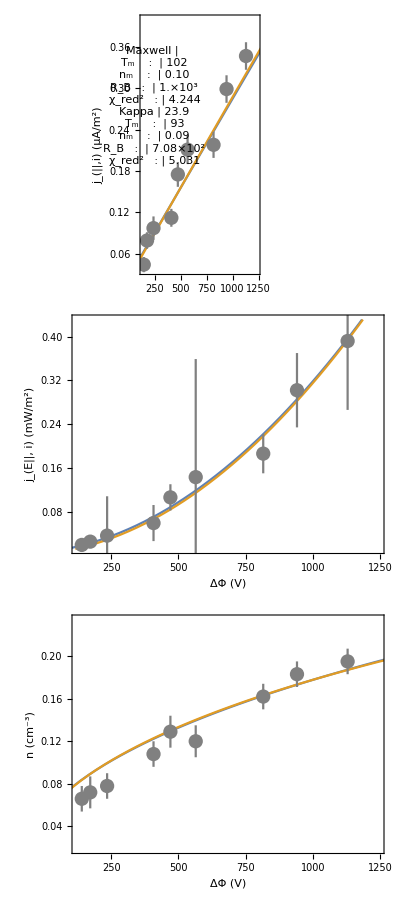

```mathematica
triplePlot=Column[{tripleJVPlot,tripleJeVPlot,tripleDensPlot}]
```

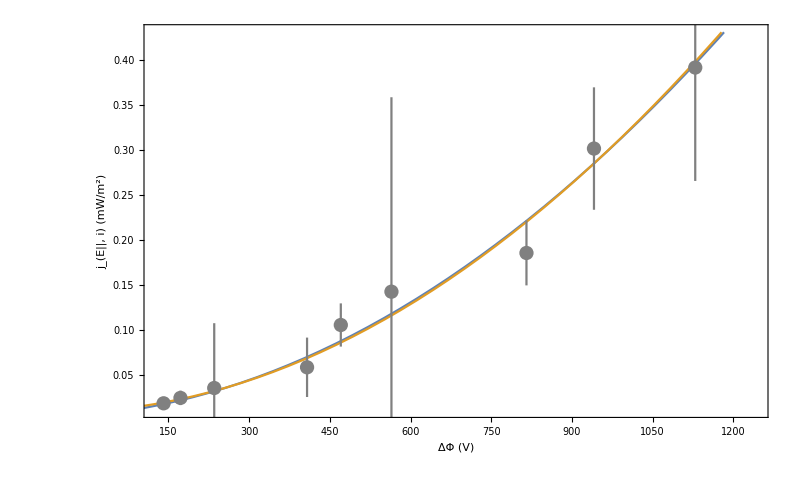
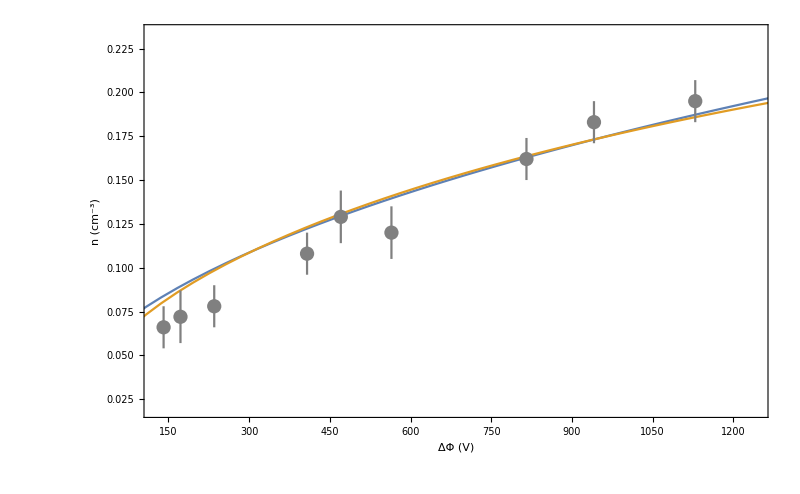
```mathematica
{{□}, {-Graphics-}, {-Graphics-}}
```

45 deg file

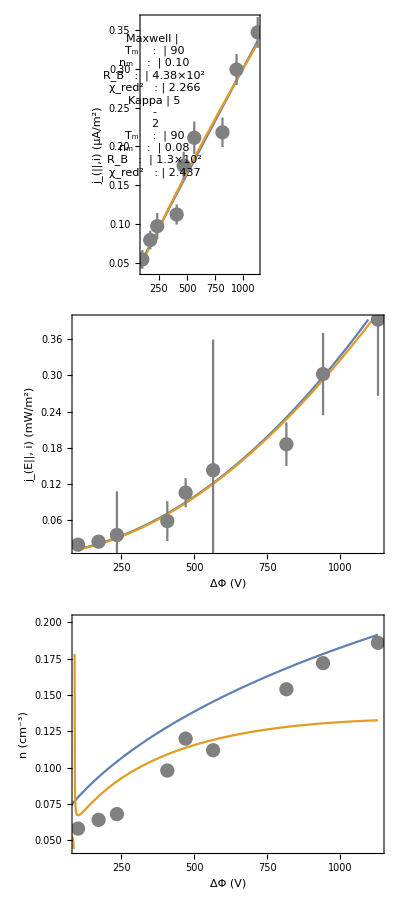

```mathematica
triplePlot=Column[{tripleJVPlot,tripleJeVPlot,tripleDensPlot}]
```

```mathematica
triplePlot=Column[{tripleJVPlot,tripleJeVPlot,tripleDensPlot}]
```

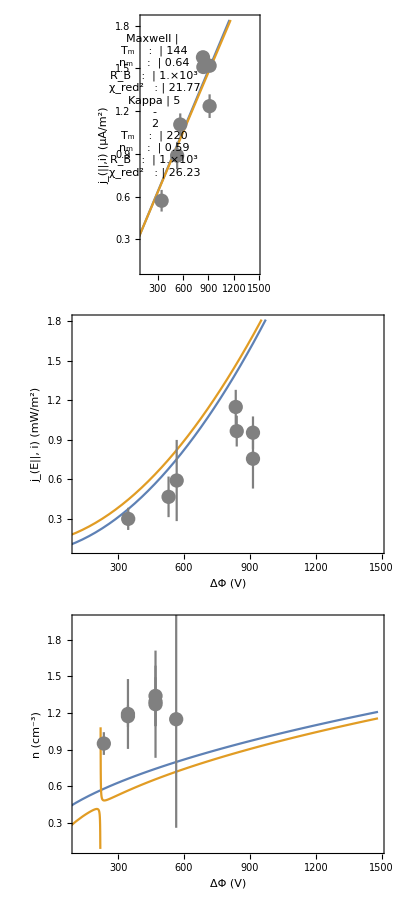

What the!? Why is kappa a better fit to the density stuff, but a terrible fit to the